```mathematica
ELestWei[shape_?NumericQ, scale_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[WeibullDistribution[shape, scale],t]*Exp[-r*t],{t,0,Infinity}]
```

```mathematica
FerrettiValues={shape->2.826, scale->5.665}
```

{shape→2.826,scale→5.665}

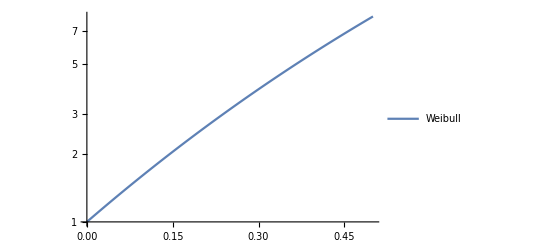

```mathematica
LogPlotWei=LogPlot[ELestWei[shape/.FerrettiValues, scale/.FerrettiValues,r],{r,0,0.5}, PlotLegends->LineLegend[{"Weibull"}]]
```

```mathematica
ELestlognorm[mu_?NumericQ, sig_?NumericQ, r_?NumericQ]:=1/NIntegrate[PDF[LogNormalDistribution[mu, sig],t]*Exp[-r*t],{t,0,Infinity}]
```

```mathematica
NishimuraValues=Solve[{PowerExpand[Log[NishimuraValues=Median[LogNormalDistribution[mu,sig]]]==Log[4]], PowerExpand[Log[Mean[LogNormalDistribution[mu, sig]]]==Log[4.7]]}, {mu,sig}][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{mu→1.38629,sig→0.567923}

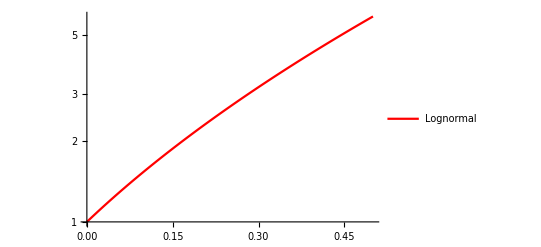

```mathematica
LogPlotlognorm=LogPlot[ELestlognorm[mu/.NishimuraValues, sig/.NishimuraValues,r],{r,0,0.5}, PlotStyle->Red, PlotLegends->LineLegend[{"Lognormal"}]]
```

```mathematica
SEIReq={D[pe[t],t]==-pe[t]/tincubation, D[pi[t],t]==+pe[t]/tincubation - pi[t]/tinfection, pe[0]==1, pi[0]==0}
```

{pe'[t]==-pe[t]/tincubation,pi'[t]==pe[t]/tincubation-pi[t]/tinfection,pe[0]==1,pi[0]==0}

```mathematica
temp=pi[t]/.DSolve[SEIReq,{pe[t], pi[t]},t][[1]]
```

(ⅇ^(-t/tincubation-t/tinfection) (-ⅇ^(t/tincubation)+ⅇ^(t/tinfection)) tinfection)/(tincubation-tinfection)

```mathematica
SEIRdistribution = Simplify[temp/Assuming[{tincubation >0, tinfection>0},Integrate[temp,{t,0,Infinity}]]]
```

(ⅇ^(-t/tincubation)-ⅇ^(-t/tinfection))/(tincubation-tinfection)

```mathematica
ELestSEIR = 1/Assuming[{tincubation >0, tinfection>0, r>0}, Integrate[SEIRdistribution * Exp[-r*t], {t,0,Infinity}]]
```

1+r tincubation+r tinfection+r^2 tincubation tinfection

```mathematica
SEIRValues={tincubation-> 3.5868, tinfection ->7.2042 }
```

{tincubation→3.5868,tinfection→7.2042}

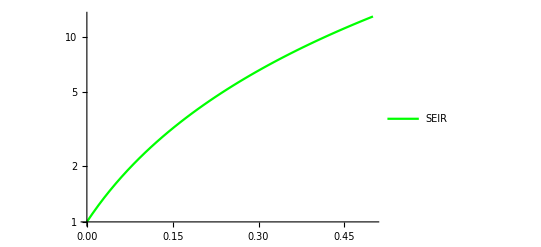

```mathematica
LogPlotSEIR=LogPlot[ELestSEIR/.SEIRValues, {r,0, 0.5}, PlotStyle->Green, PlotLegends->LineLegend[{"SEIR"}]]
```

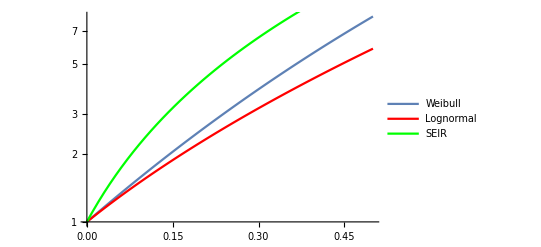

```mathematica
Show[LogPlotWei, LogPlotlognorm, LogPlotSEIR]
```